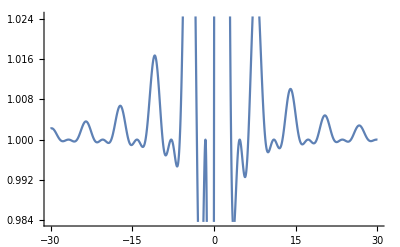

```mathematica
Plot[(x^2+1+Sin[x])/(x^2+(Cos [x])^2),{x,-30,30}]
```

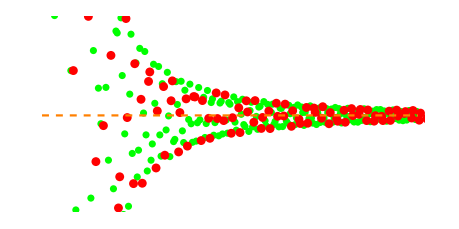

```mathematica
fx=Function[x,3Sin[x^1.1]/(x^2)+0.3];
fn=ListPlot[Table[fx[n],{n,300}],AspectRatio->1/2,PlotStyle->Green,Axes->False];
f2n=ListPlot[Table[{3n+(-1)^n,fx[3n+(-1)^n]},{n,150}],PlotStyle->Red];
fa=Plot[0.3,{x,0,300},PlotStyle->{Orange,Dashed}];
Show[fn,f2n,fa]
```

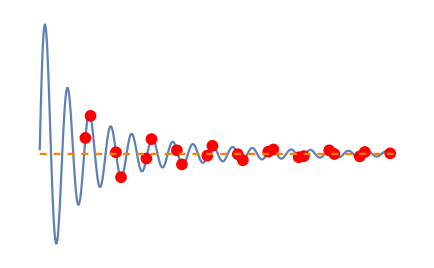

```mathematica
ff=Plot[fx[x],{x,10,80},PlotRange->All,Axes->False];
ff2n=ListPlot[Table[{3n+(-1)^n,fx[3n+(-1)^n]},{n,6,26}],PlotStyle->Red];
ffa=Plot[0.3,{x,10,80},PlotStyle->{Orange,Dashed}];
Show[ff,ff2n,ffa]
```

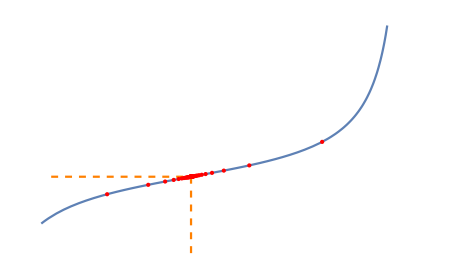

```mathematica
ft=Function[x,Tan[x/2-3]+3];
ft1=Plot[ft[x],{x,7-Pi,6+Pi},AxesOrigin->{4,0},Axes->False];
ft2=ListPlot[Table[{6+(-1)^n*30/n^2,ft[6+(-1)^n*30/n^2]},{n,90}],PlotStyle->{Red,PointSize[Medium]}];
ft3=ContourPlot[x==6,{x,5,7},{y,0,ft[6]},ContourStyle->{Orange,Dashed}];
ft4=Plot[y=ft[6],{x,4,6},PlotStyle->{Orange,Dashed}];
Show[ft1,ft3,ft4,ft2]
```

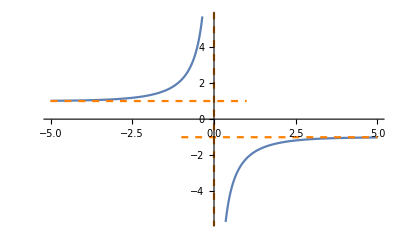

```mathematica
fp1=Plot[(1+E^x)/(1-E^x),{x,-5,5},Exclusions->{0}];
fp2=ContourPlot[x==0,{x,-1,1},{y,-6,6},ContourStyle->{Orange,Dashed}];
fp3=Plot[1,{x,-5,1},PlotStyle->{Orange,Dashed}];
fp4=Plot[-1,{x,-1,5},PlotStyle->{Orange,Dashed}];
Show[fp1,fp2,fp3,fp4]
```

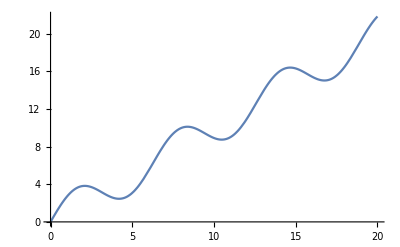

```mathematica
Plot[x+2Sin[x],{x,0,20}]
```